Номер 5:

(1+4 x^2+x^6)^(1/5) Sin[1/18+(2 x)/(√31)+(√(5+x))/7]

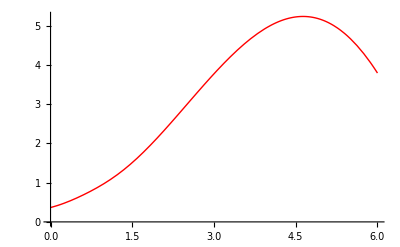

```mathematica
a=0;
b=6;
n=10;
x0=2.4316;
h=(b-a)/n;
f[x_]=(x^6+4 x^2+1)^(1/5)*Sin[(2*x/√31+1/7*√(x+5)+1/18)]
graph = Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

```mathematica
tabl=Table[{a+i* h,f[a+i* h]},{i,0,n}]//N;
TableForm[tabl]
```

0. | 0.366267
0.6 | 0.686507
1.2 | 1.17656
1.8 | 1.90721
2.4 | 2.82599
3. | 3.77226
3.6 | 4.58328
4.2 | 5.10759
4.8 | 5.21258
5.4 | 4.79492
6. | 3.79068

Номер 5 (а):

Степень многочлена, которым будет аппроксимирована функция:

```mathematica
m=1;
ACoeff1=Table[If[i+j!=0,∑_(k=0)^n (tabl[[k+1,1]])^(i+j),n+1], {i, 0, m}, {j, 0, m}]
```

{{11,33.},{33.,138.6}}

Столбец свободных членов:

```mathematica
B1:=Table[If[i!=0,∑_(k=0)^n (tabl[[k+1,2]]*(tabl[[k+1,1]])^i), ∑_(l=0)^n tabl[[l+1,2]]], {i, 0, m}];B1
```

{34.2238,134.965}

Найдём значения a_i  с  помощью встроенной функции LinearSolve:

```mathematica
A1=LinearSolve[ACoeff1,B1]
```

{0.664812,0.815482}

Тогда многочлен примет вид:

```mathematica
Q1[x_]=∑_(i=0)^m (A1[[i+1]]*x^i)
```

0.664812+0.815482 x

Изобразим полученный многочлен:

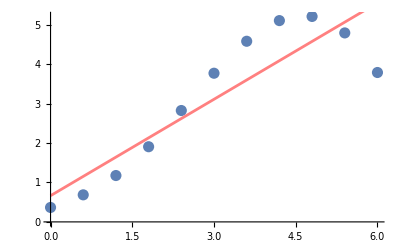

```mathematica
graphD=ListPlot[tabl,PlotStyle->{Darker,PointSize[0.02]}];
graphQ1=Plot[Q1[x],{x,a,b},PlotStyle->Pink];
Show[graphD,graphQ1]
```

Аналогичным образом найдём многочлен второй степени.

```mathematica
m=2;
ACoeff2=Table[If[i+j!=0,∑_(k=0)^n (tabl[[k+1,1]])^(i+j),n+1], {i, 0, m}, {j, 0, m}]
```

{{11,33.,138.6},{33.,138.6,653.4},{138.6,653.4,3283.16}}

```mathematica
B2:=Table[If[i!=0,∑_(k=0)^n (tabl[[k+1,2]]*(tabl[[k+1,1]])^i), ∑_(l=0)^n tabl[[l+1,2]]], {i, 0, m}];B2
```

{34.2238,134.965,604.228}

```mathematica
A2=LinearSolve[ACoeff2,B2]
```

{-0.342902,1.93516,-0.186614}

```mathematica
Q2[x_]=∑_(i=0)^m (A2[[i+1]]*x^i)
```

-0.342902+1.93516 x-0.186614 x^2

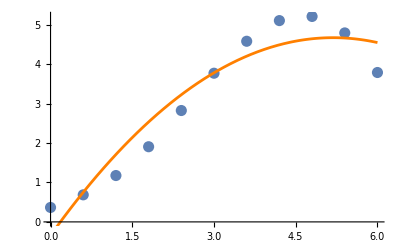

```mathematica
graphQ2=Plot[Q2[x],{x,a,b},PlotStyle->Orange];
Show[graphD,graphQ2]
```

Номер 5 (в):

```mathematica
Q3[x_]=Fit[tabl,{1,x^1,x^2,x^3},x]
Q4[x_]=Fit[tabl,{1,x^1,x^2,x^3,x^4},x]
```

0.418786-0.081898 x+0.694969 x^2-0.0979536 x^3

0.397264+0.0426528 x+0.591177 x^2-0.0702757 x^3-0.0023065 x^4

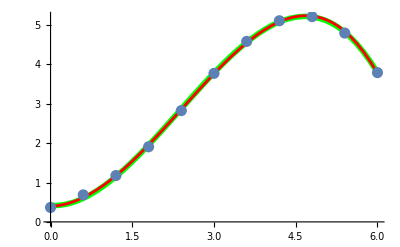

```mathematica
graphQ3=Plot[Q3[x],{x,a,b},PlotStyle->{Green,Thickness[0.01]}];
graphQ4=Plot[Q4[x],{x,a,b},PlotStyle->Red];
Show[graphQ3,graphQ4,graphD]
```

Номер 5(г):

Значения полученных многочленов в точке x0:

```mathematica
Print["Q1[x0]=",Q1[x0],", Q2[x0]=",Q2[x0],", Q3[x0]=",Q3[x0],", Q4[x0]=",Q4[x0]]
```

Q1[x0]=2.64774, Q2[x0]=3.25926, Q3[x0]=2.92047, Q4[x0]=2.90541

Номер 5(д)

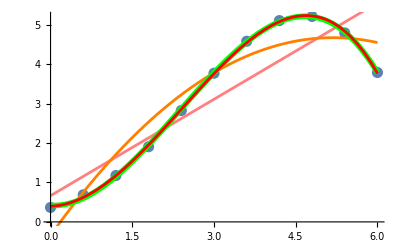

```mathematica
Show[graphD,graphQ1,graphQ2,graphQ3,graphQ4]
```

Как видно из графика, с увеличением степени многочлена аппроксимация методом наименьших квадратов даёт значения, всё более близкие к значениям исходной функции.